```mathematica
Remove["Global`*"];
ClearAll[simulatePopulations]
simulatePopulations[initialVs_,initialDoves_, initialHawks_, numLists_, numIterations_, printing_: 0] := Module[
    {V = initialVs ,doves = initialDoves, hawks = initialHawks, lists, processInteractions, 
     addToList, initializeLists, printTable = {{"Iteration","Vs", "Doves", "Hawks", 
        "Ratio of Doves","Ratio of V", "One Dove","One V", "One Hawk", "Two Doves", "Two Hawks", "D&H","twoV","VD","VH"},{0,initialVs,initialDoves,initialHawks,N[initialDoves/(initialDoves+initialHawks+initialVs)],N[initialVs/(initialDoves+initialHawks+initialVs)],0,0,0,0,0,0,0,0,0}}, 
     oneDove, oneHawk, twoDoves, twoHawks, doveAndHawk,oneV, twoV,VD,VH},
    
    initializeLists[count_] := Table[{}, {count}];
    
    addToList[listOfLists_, element_] := Module[
        {availableLists, randomIndex, updatedList = listOfLists},
        availableLists = Select[Range[Length[updatedList]], Length[updatedList[[#]]] < 2 &];
        If[Length[availableLists] > 0,
            randomIndex = RandomChoice[availableLists];    
            updatedList[[randomIndex]] = Append[updatedList[[randomIndex]], element];
            updatedList,
            Print["All lists are full."];
            listOfLists
        ]
    ];
    
    processInteractions[pairs_] := Module[{newDoves = 0,newV=0, newHawks = 0, u=RandomReal[]},
        Do[
            Switch[pair,
                {1}, newDoves += 2; oneDove++,
                {2}, newHawks += 2; oneHawk++,
{3},Null;oneV++,
                {1, 1}, newDoves += 2; twoDoves++,
{3,3},newV+=3;twoV++,
{3,2}|{2,3},newV+=1;VH++,
{3,1}|{1,3},newV+=2;newDoves++;VD++,
                (*{2, 2}, Which[u<0.25, newHawks++,u<0.5, newHawks+=2]; twoHawks++,*)
      {2, 2},Null; twoHawks++,
                {1, 2} | {2, 1},
                If[RandomReal[] < 0.5, newHawks += 1, newHawks += 2];
                If[RandomReal[] < 0.5, newDoves += 0, newDoves += 1];
                doveAndHawk++
            ],
            {pair, pairs}
        ];
        {newDoves, newHawks,newV}
    ];
    
    appendToTable[iter_, doves_, hawks_,v_] := Module[{total = doves + hawks+v, ratio, ratioV},
        ratio = If[total > 0, N[doves/total], 0];
ratioV=If[total>0,N[v/total],0];
        AppendTo[printTable, {iter,v,doves, hawks, ratio,ratioV, oneDove,oneV, oneHawk, twoDoves, twoHawks, doveAndHawk,twoV,VD,VH}]
    ];
    
    lists = initializeLists[numLists];
    
    For[i = 1, i ≤ numIterations && (doves > 0 || hawks > 0||V>0), i++,
        oneDove = 0; oneHawk = 0; twoDoves = 0; twoHawks = 0; doveAndHawk = 0;oneV=0;twoV=0;VD=0;VH=0;
        While[doves > 0 || hawks > 0||V>0,
            If[Length@Position[lists, l_List /; Length[l] < 2] == 0,
                (*Print[lists];*)
                (*Print["Failed to add elements: All lists are full."];*)
                Break[]
            ];
            rand = RandomChoice[{doves, hawks,V} -> {1, 2,3}];
            If[rand == 1,
                lists = addToList[lists, 1];
                doves--,
If[rand == 2,
                lists = addToList[lists, 2];
                hawks--,lists = addToList[lists, 3];
                V--]
            ]
        ];
        {doves, hawks,V} = processInteractions[lists];
        appendToTable[i, doves, hawks,V];
        lists = initializeLists[numLists]
    ];
    
    If[printing == 1,
        Print[Grid[printTable, Frame -> All, Alignment -> Center, 
          Background -> {None, {LightBlue, None}}]]
    ];
    
    {printTable}
]
simulatePopulations[10,10,10,100,100,1]
```

Iteration | Vs | Doves | Hawks | Ratio of Doves | Ratio of V | One Dove | One V | One Hawk | Two Doves | Two Hawks | D&H | twoV | VD | VH
0 | 10 | 10 | 10 | 0.333333 | 0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 18 | 20 | 0.473684 | 0. | 9 | 10 | 9 | 0 | 0 | 1 | 0 | 0 | 0
2 | 0 | 27 | 37 | 0.421875 | 0. | 11 | 0 | 17 | 2 | 0 | 3 | 0 | 0 | 0
3 | 0 | 38 | 56 | 0.404255 | 0. | 15 | 0 | 21 | 2 | 4 | 8 | 0 | 0 | 0
4 | 0 | 50 | 62 | 0.446429 | 0. | 18 | 0 | 24 | 5 | 11 | 10 | 0 | 0 | 0
5 | 0 | 60 | 63 | 0.487805 | 0. | 19 | 0 | 15 | 5 | 13 | 21 | 0 | 0 | 0
6 | 0 | 62 | 70 | 0.469697 | 0. | 13 | 0 | 22 | 14 | 11 | 19 | 0 | 0 | 0
7 | 0 | 63 | 80 | 0.440559 | 0. | 17 | 0 | 15 | 7 | 12 | 31 | 0 | 0 | 0
8 | 0 | 63 | 60 | 0.512195 | 0. | 10 | 0 | 17 | 18 | 23 | 17 | 0 | 0 | 0
9 | 0 | 69 | 77 | 0.472603 | 0. | 17 | 0 | 20 | 11 | 8 | 24 | 0 | 0 | 0
10 | 0 | 71 | 67 | 0.514493 | 0. | 12 | 0 | 16 | 16 | 18 | 25 | 0 | 0 | 0
11 | 0 | 68 | 82 | 0.453333 | 0. | 10 | 0 | 16 | 15 | 10 | 31 | 0 | 0 | 0
12 | 0 | 61 | 87 | 0.412162 | 0. | 8 | 0 | 22 | 15 | 15 | 30 | 0 | 0 | 0
13 | 0 | 58 | 81 | 0.417266 | 0. | 12 | 0 | 18 | 10 | 20 | 29 | 0 | 0 | 0
14 | 0 | 55 | 66 | 0.454545 | 0. | 14 | 0 | 13 | 9 | 21 | 26 | 0 | 0 | 0
15 | 0 | 51 | 69 | 0.425 | 0. | 11 | 0 | 14 | 9 | 13 | 26 | 0 | 0 | 0
16 | 0 | 51 | 69 | 0.425 | 0. | 10 | 0 | 18 | 10 | 15 | 21 | 0 | 0 | 0
17 | 0 | 56 | 73 | 0.434109 | 0. | 18 | 0 | 16 | 4 | 14 | 25 | 0 | 0 | 0
18 | 0 | 53 | 81 | 0.395522 | 0. | 8 | 0 | 25 | 14 | 14 | 20 | 0 | 0 | 0
19 | 0 | 54 | 71 | 0.432 | 0. | 11 | 0 | 19 | 11 | 21 | 20 | 0 | 0 | 0
20 | 0 | 62 | 55 | 0.529915 | 0. | 20 | 0 | 13 | 6 | 18 | 22 | 0 | 0 | 0
21 | 0 | 74 | 63 | 0.540146 | 0. | 17 | 0 | 20 | 14 | 9 | 17 | 0 | 0 | 0
22 | 0 | 78 | 58 | 0.573529 | 0. | 19 | 0 | 10 | 15 | 14 | 25 | 0 | 0 | 0
23 | 0 | 75 | 71 | 0.513699 | 0. | 12 | 0 | 14 | 19 | 8 | 28 | 0 | 0 | 0
24 | 0 | 79 | 68 | 0.537415 | 0. | 18 | 0 | 12 | 14 | 15 | 29 | 0 | 0 | 0
25 | 0 | 73 | 74 | 0.496599 | 0. | 12 | 0 | 15 | 20 | 13 | 27 | 0 | 0 | 0
26 | 0 | 73 | 72 | 0.503448 | 0. | 10 | 0 | 13 | 17 | 16 | 29 | 0 | 0 | 0
27 | 0 | 69 | 67 | 0.507353 | 0. | 13 | 0 | 14 | 16 | 15 | 28 | 0 | 0 | 0
28 | 0 | 68 | 80 | 0.459459 | 0. | 14 | 0 | 22 | 15 | 10 | 25 | 0 | 0 | 0
29 | 0 | 61 | 75 | 0.448529 | 0. | 9 | 0 | 11 | 11 | 16 | 37 | 0 | 0 | 0
30 | 0 | 65 | 70 | 0.481481 | 0. | 17 | 0 | 17 | 10 | 17 | 24 | 0 | 0 | 0
31 | 0 | 64 | 64 | 0.5 | 0. | 10 | 0 | 15 | 16 | 16 | 23 | 0 | 0 | 0
32 | 0 | 77 | 76 | 0.503268 | 0. | 21 | 0 | 27 | 13 | 10 | 17 | 0 | 0 | 0
33 | 0 | 70 | 69 | 0.503597 | 0. | 9 | 0 | 10 | 17 | 16 | 34 | 0 | 0 | 0
34 | 0 | 70 | 72 | 0.492958 | 0. | 11 | 0 | 16 | 16 | 13 | 27 | 0 | 0 | 0
35 | 0 | 61 | 79 | 0.435714 | 0. | 8 | 0 | 16 | 15 | 12 | 32 | 0 | 0 | 0
36 | 0 | 70 | 73 | 0.48951 | 0. | 17 | 0 | 21 | 11 | 18 | 22 | 0 | 0 | 0
37 | 0 | 63 | 66 | 0.488372 | 0. | 12 | 0 | 11 | 14 | 16 | 30 | 0 | 0 | 0
38 | 0 | 58 | 77 | 0.42963 | 0. | 9 | 0 | 16 | 12 | 10 | 30 | 0 | 0 | 0
39 | 0 | 64 | 79 | 0.447552 | 0. | 18 | 0 | 17 | 7 | 17 | 26 | 0 | 0 | 0
40 | 0 | 64 | 73 | 0.467153 | 0. | 14 | 0 | 15 | 11 | 18 | 28 | 0 | 0 | 0
41 | 0 | 64 | 75 | 0.460432 | 0. | 17 | 0 | 14 | 8 | 14 | 31 | 0 | 0 | 0
42 | 0 | 61 | 81 | 0.429577 | 0. | 13 | 0 | 14 | 9 | 14 | 33 | 0 | 0 | 0
43 | 0 | 50 | 88 | 0.362319 | 0. | 8 | 0 | 16 | 9 | 15 | 35 | 0 | 0 | 0
44 | 0 | 42 | 79 | 0.347107 | 0. | 8 | 0 | 20 | 7 | 20 | 28 | 0 | 0 | 0
45 | 0 | 42 | 66 | 0.388889 | 0. | 10 | 0 | 17 | 5 | 20 | 22 | 0 | 0 | 0
46 | 0 | 45 | 69 | 0.394737 | 0. | 12 | 0 | 18 | 3 | 12 | 24 | 0 | 0 | 0
47 | 0 | 48 | 74 | 0.393443 | 0. | 13 | 0 | 19 | 5 | 14 | 22 | 0 | 0 | 0
48 | 0 | 52 | 72 | 0.419355 | 0. | 14 | 0 | 20 | 6 | 16 | 22 | 0 | 0 | 0
49 | 0 | 52 | 78 | 0.4 | 0. | 14 | 0 | 24 | 8 | 13 | 22 | 0 | 0 | 0
50 | 0 | 51 | 66 | 0.435897 | 0. | 10 | 0 | 16 | 9 | 19 | 24 | 0 | 0 | 0
51 | 0 | 54 | 75 | 0.418605 | 0. | 14 | 0 | 17 | 5 | 11 | 27 | 0 | 0 | 0
52 | 0 | 50 | 77 | 0.393701 | 0. | 8 | 0 | 21 | 11 | 15 | 24 | 0 | 0 | 0
53 | 0 | 48 | 70 | 0.40678 | 0. | 9 | 0 | 20 | 11 | 19 | 19 | 0 | 0 | 0
54 | 0 | 53 | 61 | 0.464912 | 0. | 15 | 0 | 21 | 9 | 17 | 15 | 0 | 0 | 0
55 | 0 | 53 | 72 | 0.424 | 0. | 14 | 0 | 18 | 8 | 10 | 23 | 0 | 0 | 0
56 | 0 | 67 | 63 | 0.515385 | 0. | 18 | 0 | 19 | 9 | 18 | 17 | 0 | 0 | 0
57 | 0 | 68 | 71 | 0.489209 | 0. | 13 | 0 | 19 | 15 | 10 | 24 | 0 | 0 | 0
58 | 0 | 70 | 65 | 0.518519 | 0. | 16 | 0 | 13 | 13 | 16 | 26 | 0 | 0 | 0
59 | 0 | 79 | 65 | 0.548611 | 0. | 17 | 0 | 20 | 18 | 14 | 17 | 0 | 0 | 0
60 | 0 | 82 | 79 | 0.509317 | 0. | 15 | 0 | 19 | 16 | 7 | 32 | 0 | 0 | 0
61 | 0 | 84 | 77 | 0.521739 | 0. | 14 | 0 | 13 | 18 | 17 | 32 | 0 | 0 | 0
62 | 0 | 74 | 85 | 0.465409 | 0. | 11 | 0 | 16 | 18 | 12 | 37 | 0 | 0 | 0
63 | 0 | 65 | 84 | 0.436242 | 0. | 12 | 0 | 15 | 12 | 16 | 38 | 0 | 0 | 0
64 | 0 | 50 | 88 | 0.362319 | 0. | 8 | 0 | 15 | 10 | 16 | 37 | 0 | 0 | 0
65 | 0 | 50 | 79 | 0.387597 | 0. | 13 | 0 | 21 | 6 | 21 | 25 | 0 | 0 | 0
66 | 0 | 53 | 73 | 0.420635 | 0. | 12 | 0 | 21 | 9 | 19 | 20 | 0 | 0 | 0
67 | 0 | 55 | 86 | 0.390071 | 0. | 15 | 0 | 25 | 7 | 12 | 24 | 0 | 0 | 0
68 | 0 | 48 | 91 | 0.345324 | 0. | 11 | 0 | 20 | 7 | 18 | 30 | 0 | 0 | 0
69 | 0 | 49 | 71 | 0.408333 | 0. | 10 | 0 | 15 | 5 | 24 | 28 | 0 | 0 | 0
70 | 0 | 63 | 56 | 0.529412 | 0. | 18 | 0 | 14 | 6 | 19 | 19 | 0 | 0 | 0
71 | 0 | 71 | 55 | 0.563492 | 0. | 18 | 0 | 13 | 13 | 12 | 19 | 0 | 0 | 0
72 | 0 | 87 | 51 | 0.630435 | 0. | 25 | 0 | 15 | 15 | 12 | 16 | 0 | 0 | 0
73 | 0 | 92 | 64 | 0.589744 | 0. | 17 | 0 | 15 | 24 | 7 | 22 | 0 | 0 | 0
74 | 0 | 87 | 67 | 0.564935 | 0. | 11 | 0 | 13 | 27 | 12 | 27 | 0 | 0 | 0
75 | 0 | 88 | 46 | 0.656716 | 0. | 12 | 0 | 6 | 26 | 19 | 23 | 0 | 0 | 0
76 | 0 | 105 | 47 | 0.690789 | 0. | 24 | 0 | 10 | 24 | 10 | 16 | 0 | 0 | 0
77 | 0 | 111 | 54 | 0.672727 | 0. | 17 | 0 | 9 | 33 | 8 | 22 | 0 | 0 | 0
78 | 0 | 105 | 66 | 0.614035 | 0. | 13 | 0 | 6 | 31 | 6 | 36 | 0 | 0 | 0
79 | 0 | 96 | 67 | 0.588957 | 0. | 13 | 0 | 6 | 28 | 12 | 36 | 0 | 0 | 0
80 | 0 | 99 | 61 | 0.61875 | 0. | 16 | 0 | 9 | 26 | 15 | 28 | 0 | 0 | 0
81 | 0 | 89 | 83 | 0.517442 | 0. | 10 | 0 | 16 | 28 | 6 | 33 | 0 | 0 | 0
82 | 0 | 83 | 71 | 0.538961 | 0. | 9 | 0 | 9 | 22 | 19 | 36 | 0 | 0 | 0
83 | 0 | 74 | 74 | 0.5 | 0. | 14 | 0 | 10 | 17 | 13 | 35 | 0 | 0 | 0
84 | 0 | 77 | 81 | 0.487342 | 0. | 14 | 0 | 14 | 14 | 14 | 32 | 0 | 0 | 0
85 | 0 | 76 | 81 | 0.484076 | 0. | 11 | 0 | 13 | 14 | 15 | 38 | 0 | 0 | 0
86 | 0 | 68 | 71 | 0.489209 | 0. | 7 | 0 | 12 | 19 | 19 | 31 | 0 | 0 | 0
87 | 0 | 72 | 78 | 0.48 | 0. | 21 | 0 | 16 | 8 | 12 | 31 | 0 | 0 | 0
88 | 0 | 81 | 77 | 0.512658 | 0. | 19 | 0 | 17 | 12 | 16 | 29 | 0 | 0 | 0
89 | 0 | 75 | 76 | 0.496689 | 0. | 12 | 0 | 8 | 17 | 17 | 35 | 0 | 0 | 0
90 | 0 | 76 | 69 | 0.524138 | 0. | 15 | 0 | 10 | 16 | 19 | 28 | 0 | 0 | 0
91 | 0 | 79 | 53 | 0.598485 | 0. | 14 | 0 | 7 | 18 | 18 | 26 | 0 | 0 | 0
92 | 0 | 82 | 64 | 0.561644 | 0. | 14 | 0 | 14 | 21 | 8 | 23 | 0 | 0 | 0
93 | 0 | 76 | 83 | 0.477987 | 0. | 11 | 0 | 17 | 20 | 8 | 31 | 0 | 0 | 0
94 | 0 | 59 | 96 | 0.380645 | 0. | 6 | 0 | 21 | 18 | 14 | 34 | 0 | 0 | 0
95 | 0 | 44 | 94 | 0.318841 | 0. | 7 | 0 | 16 | 6 | 20 | 40 | 0 | 0 | 0
96 | 0 | 38 | 68 | 0.358491 | 0. | 9 | 0 | 17 | 5 | 26 | 25 | 0 | 0 | 0
97 | 0 | 47 | 77 | 0.379032 | 0. | 16 | 0 | 32 | 5 | 12 | 12 | 0 | 0 | 0
98 | 0 | 50 | 67 | 0.42735 | 0. | 15 | 0 | 19 | 6 | 19 | 20 | 0 | 0 | 0
99 | 0 | 50 | 71 | 0.413223 | 0. | 13 | 0 | 18 | 7 | 13 | 23 | 0 | 0 | 0
100 | 0 | 50 | 54 | 0.480769 | 0. | 12 | 0 | 13 | 9 | 19 | 20 | 0 | 0 | 0

{{{Iteration,Vs,Doves,Hawks,Ratio of Doves,Ratio of V,One Dove,One V,One Hawk,Two Doves,Two Hawks,D&H,twoV,VD,VH},{0,10,10,10,0.333333,0.333333,0,0,0,0,0,0,0,0,0},{1,0,18,20,0.473684,0.,9,10,9,0,0,1,0,0,0},{2,0,27,37,0.421875,0.,11,0,17,2,0,3,0,0,0},{3,0,38,56,0.404255,0.,15,0,21,2,4,8,0,0,0},{4,0,50,62,0.446429,0.,18,0,24,5,11,10,0,0,0},{5,0,60,63,0.487805,0.,19,0,15,5,13,21,0,0,0},{6,0,62,70,0.469697,0.,13,0,22,14,11,19,0,0,0},{7,0,63,80,0.440559,0.,17,0,15,7,12,31,0,0,0},{8,0,63,60,0.512195,0.,10,0,17,18,23,17,0,0,0},{9,0,69,77,0.472603,0.,17,0,20,11,8,24,0,0,0},{10,0,71,67,0.514493,0.,12,0,16,16,18,25,0,0,0},{11,0,68,82,0.453333,0.,10,0,16,15,10,31,0,0,0},{12,0,61,87,0.412162,0.,8,0,22,15,15,30,0,0,0},{13,0,58,81,0.417266,0.,12,0,18,10,20,29,0,0,0},{14,0,55,66,0.454545,0.,14,0,13,9,21,26,0,0,0},{15,0,51,69,0.425,0.,11,0,14,9,13,26,0,0,0},{16,0,51,69,0.425,0.,10,0,18,10,15,21,0,0,0},{17,0,56,73,0.434109,0.,18,0,16,4,14,25,0,0,0},{18,0,53,81,0.395522,0.,8,0,25,14,14,20,0,0,0},{19,0,54,71,0.432,0.,11,0,19,11,21,20,0,0,0},{20,0,62,55,0.529915,0.,20,0,13,6,18,22,0,0,0},{21,0,74,63,0.540146,0.,17,0,20,14,9,17,0,0,0},{22,0,78,58,0.573529,0.,19,0,10,15,14,25,0,0,0},{23,0,75,71,0.513699,0.,12,0,14,19,8,28,0,0,0},{24,0,79,68,0.537415,0.,18,0,12,14,15,29,0,0,0},{25,0,73,74,0.496599,0.,12,0,15,20,13,27,0,0,0},{26,0,73,72,0.503448,0.,10,0,13,17,16,29,0,0,0},{27,0,69,67,0.507353,0.,13,0,14,16,15,28,0,0,0},{28,0,68,80,0.459459,0.,14,0,22,15,10,25,0,0,0},{29,0,61,75,0.448529,0.,9,0,11,11,16,37,0,0,0},{30,0,65,70,0.481481,0.,17,0,17,10,17,24,0,0,0},{31,0,64,64,0.5,0.,10,0,15,16,16,23,0,0,0},{32,0,77,76,0.503268,0.,21,0,27,13,10,17,0,0,0},{33,0,70,69,0.503597,0.,9,0,10,17,16,34,0,0,0},{34,0,70,72,0.492958,0.,11,0,16,16,13,27,0,0,0},{35,0,61,79,0.435714,0.,8,0,16,15,12,32,0,0,0},{36,0,70,73,0.48951,0.,17,0,21,11,18,22,0,0,0},{37,0,63,66,0.488372,0.,12,0,11,14,16,30,0,0,0},{38,0,58,77,0.42963,0.,9,0,16,12,10,30,0,0,0},{39,0,64,79,0.447552,0.,18,0,17,7,17,26,0,0,0},{40,0,64,73,0.467153,0.,14,0,15,11,18,28,0,0,0},{41,0,64,75,0.460432,0.,17,0,14,8,14,31,0,0,0},{42,0,61,81,0.429577,0.,13,0,14,9,14,33,0,0,0},{43,0,50,88,0.362319,0.,8,0,16,9,15,35,0,0,0},{44,0,42,79,0.347107,0.,8,0,20,7,20,28,0,0,0},{45,0,42,66,0.388889,0.,10,0,17,5,20,22,0,0,0},{46,0,45,69,0.394737,0.,12,0,18,3,12,24,0,0,0},{47,0,48,74,0.393443,0.,13,0,19,5,14,22,0,0,0},{48,0,52,72,0.419355,0.,14,0,20,6,16,22,0,0,0},{49,0,52,78,0.4,0.,14,0,24,8,13,22,0,0,0},{50,0,51,66,0.435897,0.,10,0,16,9,19,24,0,0,0},{51,0,54,75,0.418605,0.,14,0,17,5,11,27,0,0,0},{52,0,50,77,0.393701,0.,8,0,21,11,15,24,0,0,0},{53,0,48,70,0.40678,0.,9,0,20,11,19,19,0,0,0},{54,0,53,61,0.464912,0.,15,0,21,9,17,15,0,0,0},{55,0,53,72,0.424,0.,14,0,18,8,10,23,0,0,0},{56,0,67,63,0.515385,0.,18,0,19,9,18,17,0,0,0},{57,0,68,71,0.489209,0.,13,0,19,15,10,24,0,0,0},{58,0,70,65,0.518519,0.,16,0,13,13,16,26,0,0,0},{59,0,79,65,0.548611,0.,17,0,20,18,14,17,0,0,0},{60,0,82,79,0.509317,0.,15,0,19,16,7,32,0,0,0},{61,0,84,77,0.521739,0.,14,0,13,18,17,32,0,0,0},{62,0,74,85,0.465409,0.,11,0,16,18,12,37,0,0,0},{63,0,65,84,0.436242,0.,12,0,15,12,16,38,0,0,0},{64,0,50,88,0.362319,0.,8,0,15,10,16,37,0,0,0},{65,0,50,79,0.387597,0.,13,0,21,6,21,25,0,0,0},{66,0,53,73,0.420635,0.,12,0,21,9,19,20,0,0,0},{67,0,55,86,0.390071,0.,15,0,25,7,12,24,0,0,0},{68,0,48,91,0.345324,0.,11,0,20,7,18,30,0,0,0},{69,0,49,71,0.408333,0.,10,0,15,5,24,28,0,0,0},{70,0,63,56,0.529412,0.,18,0,14,6,19,19,0,0,0},{71,0,71,55,0.563492,0.,18,0,13,13,12,19,0,0,0},{72,0,87,51,0.630435,0.,25,0,15,15,12,16,0,0,0},{73,0,92,64,0.589744,0.,17,0,15,24,7,22,0,0,0},{74,0,87,67,0.564935,0.,11,0,13,27,12,27,0,0,0},{75,0,88,46,0.656716,0.,12,0,6,26,19,23,0,0,0},{76,0,105,47,0.690789,0.,24,0,10,24,10,16,0,0,0},{77,0,111,54,0.672727,0.,17,0,9,33,8,22,0,0,0},{78,0,105,66,0.614035,0.,13,0,6,31,6,36,0,0,0},{79,0,96,67,0.588957,0.,13,0,6,28,12,36,0,0,0},{80,0,99,61,0.61875,0.,16,0,9,26,15,28,0,0,0},{81,0,89,83,0.517442,0.,10,0,16,28,6,33,0,0,0},{82,0,83,71,0.538961,0.,9,0,9,22,19,36,0,0,0},{83,0,74,74,0.5,0.,14,0,10,17,13,35,0,0,0},{84,0,77,81,0.487342,0.,14,0,14,14,14,32,0,0,0},{85,0,76,81,0.484076,0.,11,0,13,14,15,38,0,0,0},{86,0,68,71,0.489209,0.,7,0,12,19,19,31,0,0,0},{87,0,72,78,0.48,0.,21,0,16,8,12,31,0,0,0},{88,0,81,77,0.512658,0.,19,0,17,12,16,29,0,0,0},{89,0,75,76,0.496689,0.,12,0,8,17,17,35,0,0,0},{90,0,76,69,0.524138,0.,15,0,10,16,19,28,0,0,0},{91,0,79,53,0.598485,0.,14,0,7,18,18,26,0,0,0},{92,0,82,64,0.561644,0.,14,0,14,21,8,23,0,0,0},{93,0,76,83,0.477987,0.,11,0,17,20,8,31,0,0,0},{94,0,59,96,0.380645,0.,6,0,21,18,14,34,0,0,0},{95,0,44,94,0.318841,0.,7,0,16,6,20,40,0,0,0},{96,0,38,68,0.358491,0.,9,0,17,5,26,25,0,0,0},{97,0,47,77,0.379032,0.,16,0,32,5,12,12,0,0,0},{98,0,50,67,0.42735,0.,15,0,19,6,19,20,0,0,0},{99,0,50,71,0.413223,0.,13,0,18,7,13,23,0,0,0},{100,0,50,54,0.480769,0.,12,0,13,9,19,20,0,0,0}}}

```mathematica
i=20;

s1=simulatePopulations[10,10,10,60,i,0][[1]][[2;;-1,{5,6}]]
sums=Plus@@@s1
firstElements=First/@s1
```

{{0.333333,0.333333},{0.4,0.15},{0.321429,0.107143},{0.368421,0.0701754},{0.385714,0.0714286},{0.492063,0.0793651},{0.546667,0.0666667},{0.583333,0.0714286},{0.519608,0.0784314},{0.565217,0.119565},{0.610526,0.147368},{0.555556,0.194444},{0.552381,0.314286},{0.438462,0.430769},{0.326389,0.597222},{0.248447,0.726708},{0.207101,0.792899},{0.123596,0.876404},{0.0777778,0.922222},{0.0722222,0.927778},{0.0333333,0.966667}}

{0.666667,0.55,0.428571,0.438596,0.457143,0.571429,0.613333,0.654762,0.598039,0.684783,0.757895,0.75,0.866667,0.869231,0.923611,0.975155,1.,1.,1.,1.,1.}

{0.333333,0.4,0.321429,0.368421,0.385714,0.492063,0.546667,0.583333,0.519608,0.565217,0.610526,0.555556,0.552381,0.438462,0.326389,0.248447,0.207101,0.123596,0.0777778,0.0722222,0.0333333}

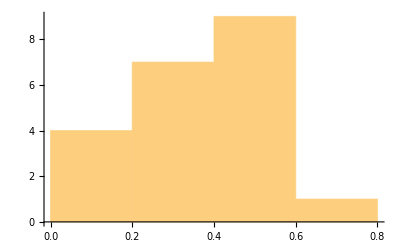

```mathematica
Histogram[firstElements]
```

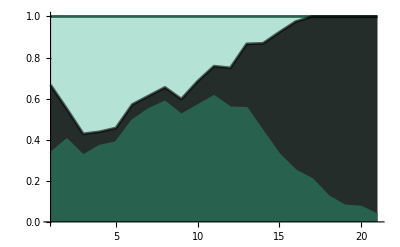

```mathematica
color1=RGBColor@@HexColorToRGB["#b4e2d4"];
color2=RGBColor@@HexColorToRGB["#f4ce14"];
color3=RGBColor@@HexColorToRGB["#1e3931"];
outlineColor=RGBColor@@HexColorToRGB["#28624e"];
lineColor=RGBColor@@HexColorToRGB["#000000"];
thickness=0.005;

p1=Plot[1,{x,1,i},Filling->Bottom,FillingStyle->color1, PlotStyle->outlineColor,AxesStyle->Directive[outlineColor,Thickness[thickness]]];
p2=ListPlot[firstElements,Joined->True,Filling->Bottom,FillingStyle->Directive[Opacity[1],outlineColor],PlotStyle->outlineColor,PlotRange->{0,1},AxesStyle->Directive[outlineColor,Thickness[thickness]]];
p3=ListPlot[sums,Joined->True,Filling->Bottom,FillingStyle->Directive[Opacity[0.8],Black],PlotRange->{0,1},PlotStyle->Directive[Opacity[0.6],Black],AxesStyle->Directive[outlineColor,Thickness[thickness]]];


Show[p1,p3,p2,PlotRange->{0,1},PlotStyle->lineColor]
```